Άσκηση 3

Να μελετηθεί το σύστημα {x'=x-y^2+μ x^2
y'=y+x^2.

Το σύστημα αυτό δεν λύνεται αναλυτικά (όπως φαίνεται αν δοκιμάσουμε την DSolve), επομένως προχωράμε σε αριθμητική λύση.

Ορίζουμε τις συναρτήσεις στα δεξιά μέλη των εξισώσεων.

```mathematica
ClearAll["Global`*"]
f[x_,y_]:=-x-y^2+μ x^2;
g[x_,y_]:=y+x^2;
```

Σημεία Ισορροπίας

Υπολογίζουμε τα σημεία ισορροπίας του συστήματος.

```mathematica
eqPts=Solve[{-x-y^2+μ x^2==0,y+x^2==0},{x,y}];
```

Σχεδιάζουμε το διάγραμμα διακλάδωσης, για να δούμε την εξέλιξη των σημείων ισορροπίας ως συνάρτηση του μ.

```mathematica
(* βοηθητική συνάρτηση του υπολογισμού των σημείων ισορροπίας για δεδομένο μ *)
eqPtsN[m_]:=Map[Re[#[[All,2]]]&,
Cases[eqPts/.μ->m//N,
x_/;And[Abs@Im@x[[1,2]]<=10^-13,Abs@Im@x[[2,2]]<=10^-13]]
,{1}];
(* δημιουργία λίστας των μ *)
ms=Table[i,{i,-8,8,0.1}];
(* υπολογισμός των σημείων *)
points=Reap[
For[i=1,i≤Length[ms],i++,
m=ms[[i]];
pt=Quiet@eqPtsN[m];
Sow@Map[Prepend[#,m]&,pt]
]
][[2,1]];
(* σχεδιασμός του διαγράμματος διακλάδωσης *)
Graphics3D[
{Black,PointSize[0.005],Point[Flatten[points,1]],
Red,PointSize[0.01],Point[{0,0,0}]},
Axes->True,
AxesLabel->{"μ","x","y"},
AxesOrigin->{0,0,0},
ImageSize->Large
]
```

-Graphics3D-

Όπως φαίνεται, έχουμε 2 σημεία ισορροπίας για μ<2 (περίπου), τα οποία γίνονται 3 και έπειτα 4.
Επίσης, για μ=0 έχουμε μόνο 1 σημείο ισορροπίας, το (0,0).
Για μ<0 βρίσκουμε γενικά 2 σημεία, τα οποία όμως όσο το μ μικραίνει πλησιάζουν μεταξύ τους στο (0,0).

```mathematica
Quiet@eqPtsN[0]
```

{{0.,0.}}

```mathematica
eqPtsN[1]
```

{{0.,0.},{-1.32472,-1.75488}}

```mathematica
eqPtsN[-2]
```

{{0.,0.},{-0.453398,-0.205569}}

```mathematica
eqPtsN[2]
```

{{0.,0.},{1.,-1.},{-1.61803,-2.61803},{0.618034,-0.381966}}

```mathematica
eqPtsN[2.1]
```

{{0.,0.},{1.08584,-1.17906},{-1.64551,-2.70771},{0.559669,-0.313229}}

Ευστάθεια

Διερευνούμε την ευστάθεια των σημείων ισορροπίας.
Βρίσκουμε τον πίνακα του γραμμικοποιημένου συστήματος.

```mathematica
A={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}};
StringForm["A = ``",MatrixForm[A]]
```

A = (-1+2 x μ | -2 y
2 x | 1)

ο οποίος έχει ιδιοτιμές

```mathematica
λ=Eigenvalues[A];
StringForm["λ_1 = ``\nλ_2 = ``",λ[[1]],λ[[2]]]
```

λ_1 = x μ-√(1-4 x y-2 x μ+x^2 μ^2)
λ_2 = x μ+√(1-4 x y-2 x μ+x^2 μ^2)

μ=0

Για το σημείο (0,0) έχουμε

```mathematica
A/.{x->0,y->0,μ->0}//MatrixForm
λ/.{x->0,y->0,μ->0}
```

(-1 | 0
0 | 1)

{-1,1}

Επομένως το (0,0) είναι σάγμα.

μ<0

Για μ<0 έχουμε γενικά δύο σημεία ισορροπίας. Για παράδειγμα για μ=-1 έχουμε τα:

```mathematica
pt1=eqPtsN[-1]
```

{{0.,0.},{-0.682328,-0.465571}}

Για το σημείο (0,0) έχουμε

```mathematica
A/.{x->pt1[[1,1]],y->pt1[[1,2]],μ->-1}//MatrixForm
λ/.{x->pt1[[1,1]],y->pt1[[1,2]],μ->-1}
```

(-1. | 0.
0. | 1)

{-1.,1.}

που σημαίνει ότι είναι και πάλι σάγμα.

Το 2ο σημείο έχει:

```mathematica
A/.{x->pt1[[2,1]],y->pt1[[2,2]],μ->-1}//MatrixForm
λ/.{x->pt1[[2,1]],y->pt1[[2,2]],μ->-1}
```

(0.364656 | 0.931142
-1.36466 | 1)

{0.682328-1.08156 ⅈ,0.682328+1.08156 ⅈ}

επομένως είναι μια ασταθής εστία.

0<μ<2

Για 0<μ<2 έχουμε γενικά δύο σημεία ισορροπίας. Για παράδειγμα για μ=1 έχουμε τα:

```mathematica
pt2=eqPtsN[1]
```

{{0.,0.},{-1.32472,-1.75488}}

Για το σημείο (0,0) έχουμε

```mathematica
A/.{x->pt2[[1,1]],y->pt2[[1,2]],μ->1}//MatrixForm
λ/.{x->pt2[[1,1]],y->pt2[[1,2]],μ->1}
```

(-1. | 0.
0. | 1)

{-1.,1.}

που σημαίνει ότι είναι και πάλι σάγμα.

Το 2ο σημείο έχει:

```mathematica
A/.{x->pt2[[2,1]],y->pt2[[2,2]],μ->1}//MatrixForm
λ/.{x->pt2[[2,1]],y->pt2[[2,2]],μ->1}
```

(-3.64944 | 3.50976
-2.64944 | 1)

{-1.32472-1.97346 ⅈ,-1.32472+1.97346 ⅈ}

επομένως είναι μια ευσταθής εστία.

μ=2

Για μ=2 (και μια μικρή περιοχή γύρω του) έχουμε τρία σημεία ισορροπίας.

```mathematica
pt3=eqPtsN[2]
```

{{0.,0.},{1.,-1.},{-1.61803,-2.61803},{0.618034,-0.381966}}

Για το σημείο (0,0) έχουμε

```mathematica
A/.{x->pt3[[1,1]],y->pt3[[1,2]],μ->2}//MatrixForm
λ/.{x->pt3[[1,1]],y->pt3[[1,2]],μ->2}
```

(-1. | 0.
0. | 1)

{-1.,1.}

που σημαίνει ότι είναι και πάλι σάγμα.

Το 2ο σημείο έχει:

```mathematica
A/.{x->pt3[[2,1]],y->pt3[[2,2]],μ->2}//MatrixForm
λ/.{x->pt3[[2,1]],y->pt3[[2,2]],μ->2}
```

(3. | 2.
2. | 1)

{-0.236068,4.23607}

επομένως είναι σάγμα.

Το 3ο σημείο έχει:

```mathematica
A/.{x->pt3[[3,1]],y->pt3[[3,2]],μ->2}//MatrixForm
λ/.{x->pt3[[3,1]],y->pt3[[3,2]],μ->2}
```

(-7.47214 | 5.23607
-3.23607 | 1)

{-4.23607,-2.23607}

επομένως είναι ευσταθής κόμβος.

μ>2

Για μ>2 έχουμε τέσσερα σημεία ισορροπίας. Για παράδειγμα, για μ=3:

```mathematica
pt4=eqPtsN[3]
```

{{0.,0.},{1.53209,-2.3473},{-1.87939,-3.53209},{0.347296,-0.120615}}

Για το σημείο (0,0) έχουμε

```mathematica
A/.{x->pt4[[1,1]],y->pt4[[1,2]],μ->3}//MatrixForm
λ/.{x->pt4[[1,1]],y->pt4[[1,2]],μ->3}
```

(-1. | 0.
0. | 1)

{-1.,1.}

που σημαίνει ότι είναι και πάλι σάγμα.

Το 2ο σημείο έχει:

```mathematica
A/.{x->pt4[[2,1]],y->pt4[[2,2]],μ->3}//MatrixForm
λ/.{x->pt4[[2,1]],y->pt4[[2,2]],μ->3}
```

(8.19253 | 4.69459
3.06418 | 1)

{-0.630415,9.82295}

επομένως είναι σάγμα.

Το 3ο σημείο έχει:

```mathematica
A/.{x->pt4[[3,1]],y->pt4[[3,2]],μ->3}//MatrixForm
λ/.{x->pt4[[3,1]],y->pt4[[3,2]],μ->3}
```

(-12.2763 | 7.06418
-3.75877 | 1)

{-9.82295,-1.45336}

επομένως είναι ευσταθής κόμβος.

Το 4ο σημείο έχει:

```mathematica
A/.{x->pt4[[4,1]],y->pt4[[4,2]],μ->3}//MatrixForm
λ/.{x->pt4[[4,1]],y->pt4[[4,2]],μ->3}
```

(1.08378 | 0.24123
0.694593 | 1)

{0.630415,1.45336}

επομένως είναι ασταθής κόμβος.

Vector Field

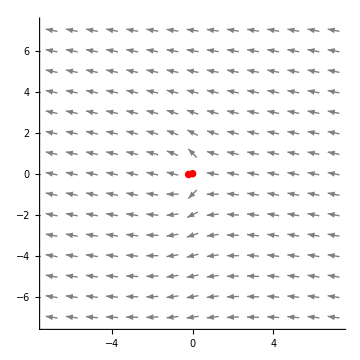
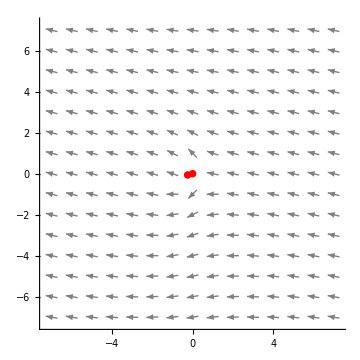
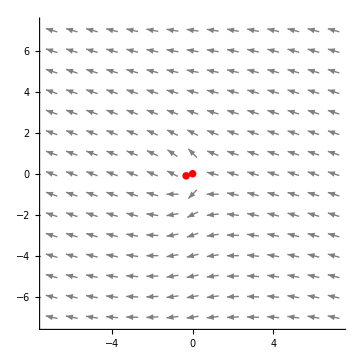
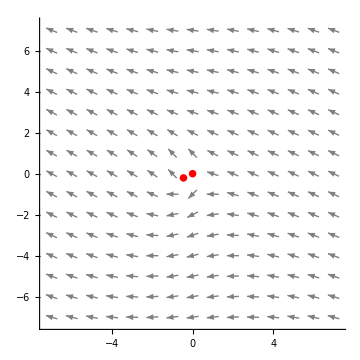
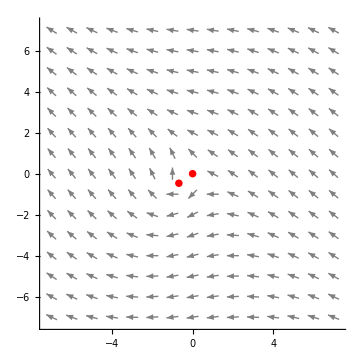
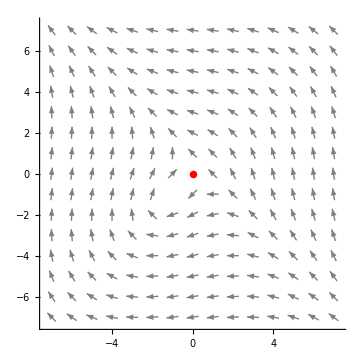
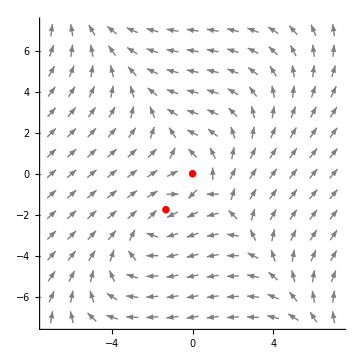
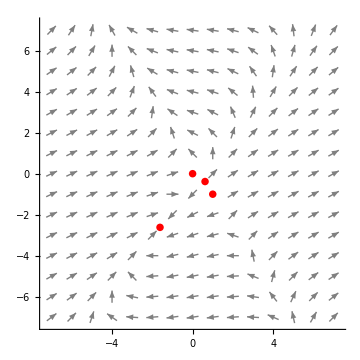
μ = -5 | -Graphics-
μ = -4 | -Graphics-
μ = -3 | -Graphics-
μ = -2 | -Graphics-
μ = -1 | -Graphics-
μ = 0 | -Graphics-
μ = 1 | -Graphics-
μ = 2 | -Graphics-
μ = 3 | -Graphics-
μ = 4 | -Graphics-
μ = 5 | -Graphics-

```mathematica
aaa=7;
vectorfields=Table[
{
StringForm["μ = ``",i],
VectorPlot[{f[x,y],g[x,y]}/.μ->i,{x,-aaa,aaa},{y,-aaa,aaa},
VectorScale->{0.03,1,None},
Frame->None,
VectorStyle->{Red, Gray},
Axes->True,
ImageSize->Medium,
Epilog->{Red,PointSize[0.015],Point[Quiet@eqPtsN[i]]}
]
}
,{i,-5,5}];
TableForm[vectorfields]
```

Από τα παραπάνω διαγράμματα φαίνεται πως αλλάζει η συμπεριφορά του συστήματος καθώς αλλάζει το μ.

Χώρος των Φάσεων

Σχεδιάζουμε το διάγραμμα φάσεων για διάφορα μ.

Ορίζουμε τις διαφορικές εξισώσεις.

```mathematica
deq1=x'[t]==-x[t]-y[t]^2+μ x[t]^2;
deq2=y'[t]==y[t]+x[t]^2;
```

Ορίζουμε τις παραμέτρους.

```mathematica
tmin=0;
tmax=500;
```

Σχεδιάζουμε κάποιες τροχιές, τα σημεία ισορροπίας, και το διανυσματικό πεδίο στο ίδιο διάγραμμα.

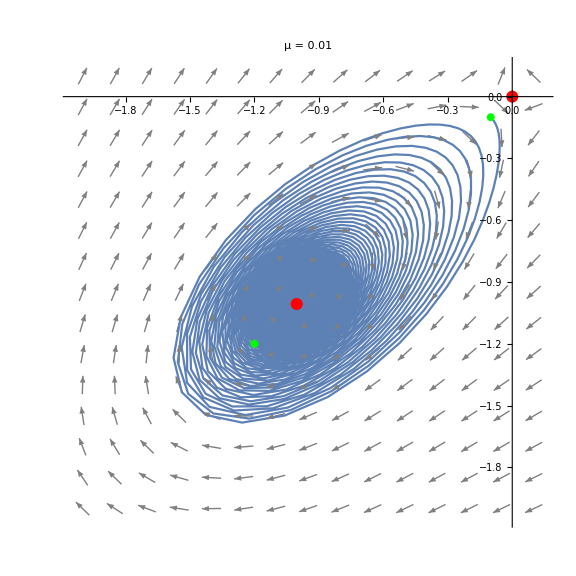

```mathematica
(*ορίζουμε το μ*)
m=0.01;
(* ορίζουμε τις αρχικές συνθήκες *)
initialConditions={{-0.1,-0.1},{-1.2,-1.2}};
(* υπολογίζουμε τα σημεία ισορροπίας *)
pts=eqPtsN[m];
(* σχεδιάζουμε το διανυσματικό πεδίο και τα σημεία ισορροπίας *)
xmin=-2;xmax=0.1;ymin=-2;ymax=0.1;
vectorfield=VectorPlot[{f[x,y],g[x,y]}/.μ->m,{x,xmin,xmax},{y,ymin,ymax},
VectorScale->{0.03,1,None},
Frame->None,
VectorStyle->{Red, Gray},
Axes->True,
AxesOrigin->{0,0},
Epilog->{Red,PointSize[0.015],Point[pts],Green,PointSize[0.01],Point[initialConditions]}
];
(* σχεδιάζουμε τις τροχιές *)
trajectories=Reap@
For[i=1,i≤Length[initialConditions],i++,
IVP={deq1/.μ->m,deq2,x[0]==initialConditions[[i,1]],y[0]==initialConditions[[i,2]]};
sol=Quiet@NDSolve[IVP,{x,y},{t,tmin,tmax}];
xt[t_]:=x[t]/.sol[[1]];
yt[t_]:=y[t]/.sol[[1]];
Sow@ParametricPlot[{xt[t],yt[t]},{t,tmin,tmax},
PlotRange->All,
ImageSize->Medium
]
]//Last//First;
(* βάζουμε όλα τα διαγράμματα μαζί *)
Show[
vectorfield,trajectories,
ImageSize->Large,
PlotLabel->StringForm["μ = ``",m]
]
```

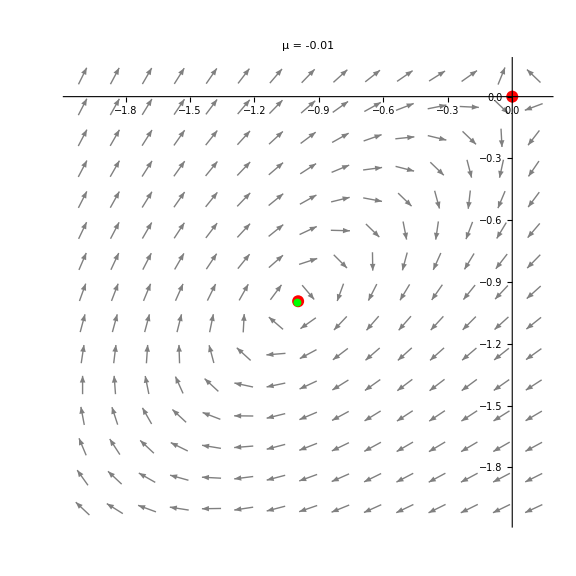

```mathematica
(*ορίζουμε το μ*)
m=-0.01;
(* ορίζουμε τις αρχικές συνθήκες *)
initialConditions={{-1,-1}};
(* υπολογίζουμε τα σημεία ισορροπίας *)
pts=eqPtsN[m];
(* σχεδιάζουμε το διανυσματικό πεδίο και τα σημεία ισορροπίας *)
xmin=-2;xmax=0.1;ymin=-2;ymax=0.1;
vectorfield=VectorPlot[{f[x,y],g[x,y]}/.μ->m,{x,xmin,xmax},{y,ymin,ymax},
VectorScale->{0.03,1,None},
Frame->None,
VectorStyle->{Red, Gray},
Axes->True,
AxesOrigin->{0,0},
Epilog->{Red,PointSize[0.015],Point[pts],Green,PointSize[0.01],Point[initialConditions]}
];
(* σχεδιάζουμε τις τροχιές *)
trajectories=Reap@
For[i=1,i≤Length[initialConditions],i++,
IVP={deq1/.μ->m,deq2,x[0]==initialConditions[[i,1]],y[0]==initialConditions[[i,2]]};
sol=Quiet@NDSolve[IVP,{x,y},{t,tmin,tmax}];
xt[t_]:=x[t]/.sol[[1]];
yt[t_]:=y[t]/.sol[[1]];
Sow@ParametricPlot[{xt[t],yt[t]},{t,tmin,tmax},
PlotRange->All,
ImageSize->Medium
]
]//Last//First;
(* βάζουμε όλα τα διαγράμματα μαζί *)
Show[
vectorfield,trajectories,
ImageSize->Large,
PlotLabel->StringForm["μ = ``",m]
]
```

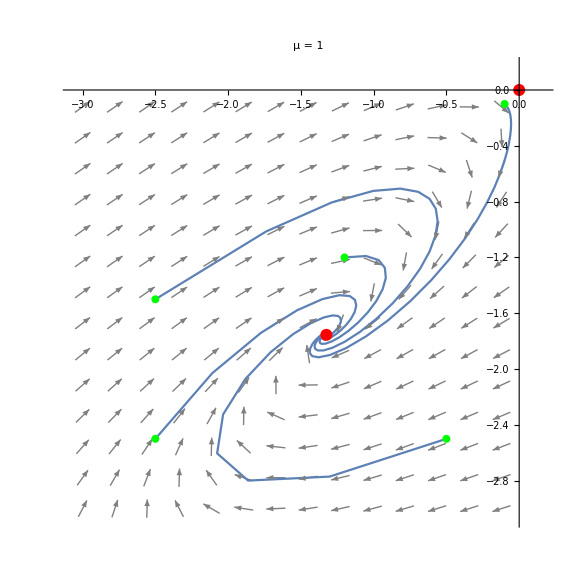

```mathematica
(*ορίζουμε το μ*)
m=1;
(* ορίζουμε τις αρχικές συνθήκες *)
initialConditions={{-0.1,-0.1},{-1.2,-1.2},{-2.5,-2.5},{-2.5,-1.5},{-0.5,-2.5}};
(* υπολογίζουμε τα σημεία ισορροπίας *)
pts=eqPtsN[m];
(* σχεδιάζουμε το διανυσματικό πεδίο και τα σημεία ισορροπίας *)
xmin=-3;xmax=0.1;ymin=-3;ymax=0.1;
vectorfield=VectorPlot[{f[x,y],g[x,y]}/.μ->m,{x,xmin,xmax},{y,ymin,ymax},
VectorScale->{0.03,1,None},
Frame->None,
VectorStyle->{Red, Gray},
Axes->True,
AxesOrigin->{0,0},
Epilog->{Red,PointSize[0.015],Point[pts],Green,PointSize[0.01],Point[initialConditions]}
];
(* σχεδιάζουμε τις τροχιές *)
trajectories=Reap@
For[i=1,i≤Length[initialConditions],i++,
IVP={deq1/.μ->m,deq2,x[0]==initialConditions[[i,1]],y[0]==initialConditions[[i,2]]};
sol=Quiet@NDSolve[IVP,{x,y},{t,tmin,tmax}];
xt[t_]:=x[t]/.sol[[1]];
yt[t_]:=y[t]/.sol[[1]];
Sow@ParametricPlot[{xt[t],yt[t]},{t,tmin,tmax},
PlotRange->All,
ImageSize->Medium
]
]//Last//First;
(* βάζουμε όλα τα διαγράμματα μαζί *)
Show[
vectorfield,trajectories,
ImageSize->Large,
PlotLabel->StringForm["μ = ``",m]
]
```

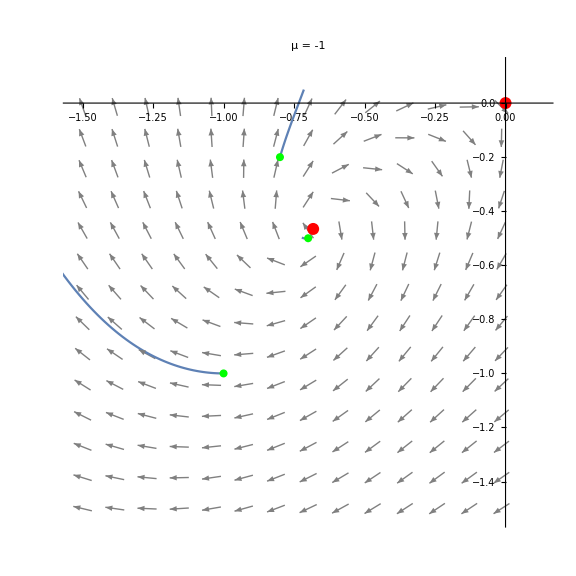

```mathematica
(*ορίζουμε το μ*)
m=-1;
(* ορίζουμε τις αρχικές συνθήκες *)
initialConditions={{-1,-1},{-0.8,-0.2},{-0.7,-0.5}};
(* υπολογίζουμε τα σημεία ισορροπίας *)
pts=eqPtsN[m];
(* σχεδιάζουμε το διανυσματικό πεδίο και τα σημεία ισορροπίας *)
xmin=-1.5;xmax=0.1;ymin=-1.5;ymax=0.1;
vectorfield=VectorPlot[{f[x,y],g[x,y]}/.μ->m,{x,xmin,xmax},{y,ymin,ymax},
VectorScale->{0.03,1,None},
Frame->None,
VectorStyle->{Red, Gray},
Axes->True,
AxesOrigin->{0,0},
Epilog->{Red,PointSize[0.015],Point[pts],Green,PointSize[0.01],Point[initialConditions]}
];
(* σχεδιάζουμε τις τροχιές *)
trajectories=Reap@
For[i=1,i≤Length[initialConditions],i++,
IVP={deq1/.μ->m,deq2,x[0]==initialConditions[[i,1]],y[0]==initialConditions[[i,2]]};
sol=Quiet@NDSolve[IVP,{x,y},{t,tmin,0.001tmax}];
xt[t_]:=x[t]/.sol[[1]];
yt[t_]:=y[t]/.sol[[1]];
Sow@ParametricPlot[{xt[t],yt[t]},{t,tmin,0.001tmax},
PlotRange->All,
ImageSize->Medium
]
]//Last//First;
(* βάζουμε όλα τα διαγράμματα μαζί *)
Show[
vectorfield,trajectories,
ImageSize->Large,
PlotLabel->StringForm["μ = ``",m]
]
```

Δεν μπόρεσα να σχεδιάσω τροχιές στην ασταθή εστία...
Πρέπει να σχεδιαστεί το κάθε διάγραμμα φάσης ξεχωριστά, γιατί οι τροχιές απομακρύνονται πολύ γρήγορα από το σημείο ισορροπίας, επομένως χρειάζονται πολύ μικρά όρια ολοκλήρωσης ανάλογα με το αρχικό σημείο.

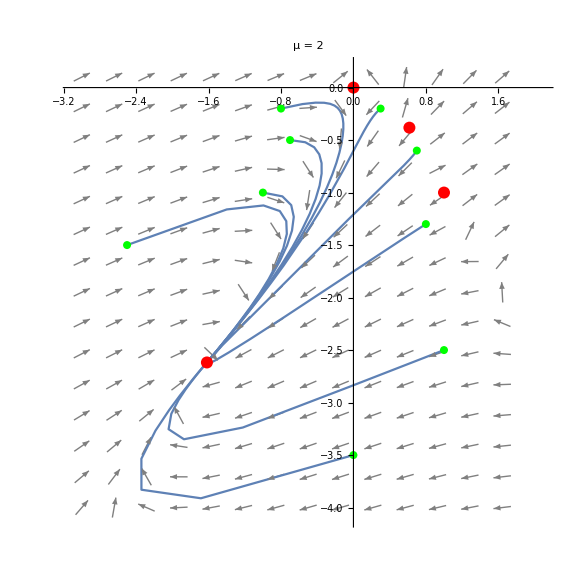

```mathematica
(*ορίζουμε το μ*)
m=2;
(* ορίζουμε τις αρχικές συνθήκες *)
initialConditions={{-1,-1},{-0.8,-0.2},{-0.7,-0.5},{0.3,-0.2},{0.7,-0.6},{0.8,-1.3},{1,-2.5},{0,-3.5},{-2.5,-1.5}};
(* υπολογίζουμε τα σημεία ισορροπίας *)
pts=eqPtsN[m];
(* σχεδιάζουμε το διανυσματικό πεδίο και τα σημεία ισορροπίας *)
xmin=-3;xmax=2;ymin=-4;ymax=0.1;
vectorfield=VectorPlot[{f[x,y],g[x,y]}/.μ->m,{x,xmin,xmax},{y,ymin,ymax},
VectorScale->{0.03,1,None},
Frame->None,
VectorStyle->{Red, Gray},
Axes->True,
AxesOrigin->{0,0},
Epilog->{Red,PointSize[0.015],Point[pts],Green,PointSize[0.01],Point[initialConditions]}
];
(* σχεδιάζουμε τις τροχιές *)
trajectories=Reap@
For[i=1,i≤Length[initialConditions],i++,
IVP={deq1/.μ->m,deq2,x[0]==initialConditions[[i,1]],y[0]==initialConditions[[i,2]]};
sol=Quiet@NDSolve[IVP,{x,y},{t,tmin,tmax}];
xt[t_]:=x[t]/.sol[[1]];
yt[t_]:=y[t]/.sol[[1]];
Sow@ParametricPlot[{xt[t],yt[t]},{t,tmin,tmax},
PlotRange->All,
ImageSize->Medium
]
]//Last//First;
(* βάζουμε όλα τα διαγράμματα μαζί *)
Show[
vectorfield,trajectories,
ImageSize->Large,
PlotLabel->StringForm["μ = ``",m]
]
```